```mathematica
dt=1/365;
```

```mathematica
A=FinancialData["^DJI","Jan. 1, 2008"][[1;;576/2]];
```

```mathematica
A=FinancialData["IFX.DE","Jan. 1, 2000"];
```

```mathematica
A=FinancialData["GE","Jan. 1, 2000"];
```

```mathematica
A=FinancialData["NYSE:MHP","Jan. 1, 2007"];
```

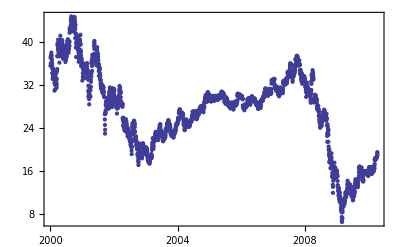

```mathematica
DateListPlot[A]
```

```mathematica
B=Differences[ Log[Transpose[A]][[2]]]/Sqrt[dt];
Sqrt[Variance[B]]
B=(B-Mean[B])/Sqrt[Variance[B]];
```

0.589266

```mathematica
Histogram[B,PlotRange->All]
```

-Graphics-

```mathematica
2
```

```mathematica
Skewness[B]
Kurtosis[B]
100(-Sqrt[Kurtosis[B]-1-Skewness[B]^2]+Sqrt[Kurtosis[B]-1])/Sqrt[Kurtosis[B]-1]
```

0.371081

8.68144

0.900375

```mathematica
Kurtosis[B]
```